# Non-Unitary Dynamics of Quantum States: Figures

```mathematica
Quit[]
```

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

## How Statistical Mixture Arises

Let us consider a total system consisting of two qubits, one representing the “system” and the other the “environment”.

```mathematica
SS=S[{1,2},None]
```

{S_1,S_2}

Initially, the total system is assumed to be in a product state.

```mathematica
in=Ket[];
LogicalForm[in,SS]
```

0_S_10_S_2

Suppose that we want to perform a single-qubit rotation around the x-axis. The required Hamiltonian of the system involves the Pauli-X operator.

```mathematica
H0=S[1,1]*Ω/2;
H0//PauliForm
```

(X Ω)/2

We choose Ω as our basic energy scale to measure all other energies  and time.

```mathematica
Ω=1
```

1

Unfortunately, the system is coupled to the environment via the Ising-type YY interaction. Here, J is the coupling constant.

```mathematica
Hint=J/2*S[1,2]**S[2,2];
Hint//PauliForm
Let[Real,J]
```

(J Y⊗Y)/2

This the total Hamiltonian of the total system.

```mathematica
HH=H0+Hint;
HH//PauliForm
```

(X⊗I)/2+(J Y⊗Y)/2

The evolution of the total system as a closed system is governed by this time-evolution operator.

```mathematica
U[t_]=MultiplyExp[-I*t*HH]//Elaborate;
U[t]//PauliForm
Let[Real,t]
```

1/2 ⅇ^(-1/2 ⅈ √(1+J^2) t) (1+ⅇ^(ⅈ √(1+J^2) t)) I⊗I-(ⅇ^(-1/2 ⅈ √(1+J^2) t) (-1+ⅇ^(ⅈ √(1+J^2) t)) X⊗I)/(2 √(1+J^2))-(ⅇ^(-1/2 ⅈ √(1+J^2) t) (-1+ⅇ^(ⅈ √(1+J^2) t)) J Y⊗Y)/(2 √(1+J^2))

The above expression looks simpler with the trigonometric functions than the exponential function.

```mathematica
U[t_]=MultiplyExp[-I*t*HH]//Elaborate//ExpToTrig;
U[t]//PauliForm
```

-(X⊗I (Cos[1/2 √(1+J^2) t]-ⅈ Sin[1/2 √(1+J^2) t]) (-1+Cos[√(1+J^2) t]+ⅈ Sin[√(1+J^2) t]))/(2 √(1+J^2))-(J Y⊗Y (Cos[1/2 √(1+J^2) t]-ⅈ Sin[1/2 √(1+J^2) t]) (-1+Cos[√(1+J^2) t]+ⅈ Sin[√(1+J^2) t]))/(2 √(1+J^2))+1/2 I⊗I (Cos[1/2 √(1+J^2) t]-ⅈ Sin[1/2 √(1+J^2) t]) (1+Cos[√(1+J^2) t]+ⅈ Sin[√(1+J^2) t])

## Kraus Operators

```mathematica
Let[Complex,c]
```

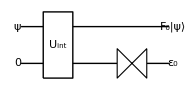

```mathematica
qc0=QuantumCircuit[
LogicalForm[ProductState[S[1]->c@{0,1},S[2]->{1,0},"Label"->{Ket["ψ"],Automatic}],SS],
{U[t],"Label"->"U_int"},"Spacer",
Projector[Ket[S[2]->0],S[2]],
{Ket[S[1]->1],"Label"->"F_0|ψ⟩"},
{Ket[S[2]->1],"Label"->Ket["ε_0"]}
]
```

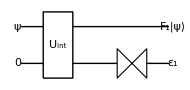

```mathematica
qc1=QuantumCircuit[
LogicalForm[ProductState[S[1]->c@{0,1},S[2]->{1,0},"Label"->{Ket["ψ"],Automatic}],SS],
{U[t],"Label"->"U_int"},"Spacer",
Projector[Ket[S[2]->1],S[2]],
{Ket[S[1]->1],"Label"->"F_1|ψ⟩"},
{Ket[S[2]->1],"Label"->Ket["ε_1"]}
]
```